## Generate Random Process

```mathematica
SetDirectory[NotebookDirectory[]];
Get["ProcessWithExpACF`"]
λ=50;
Δt=1/10000;
length = 5 10^6;
x0=1;
𝒟=ChiSquareDistribution[ν=3];
vals=RandomVariateExpACF[𝒟,length,Δt,λ,x0];
```

## Verify Autocovariance Function

-Graphics-

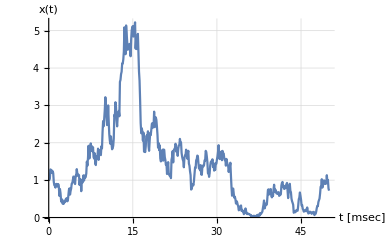

```mathematica
normFactor = CovarianceFunction[vals,0];
autocorrelationPlot=ListLinePlot[
{ParallelTable[{z Δt 10^3,CovarianceFunction[vals,z]/normFactor},{z,0,500,20}],
Table[{z Δt 10^3,Exp[-z Δt λ ]},{z,0,500,20}]},PlotRange->Full,GridLines->Automatic,
PlotLegends->Placed[{"Simulation","Exp[-λτ]"},{.8,.8}],AxesLabel->{"τ [msec]","C_xx(τ)"},LabelStyle -> Directive[Black,13,FontFamily->"Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],PlotMarkers->{{Graphics[{Disk[]}],.04},""}]
timePlot=ListLinePlot[Thread[{Table[Δt x,{x,1,500}] 10^3,vals[[1;;500]]}],LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],
AxesLabel->{"t [msec]","x(t)"},GridLines->Automatic
]
```

## Verify PDF

Note: The PDF estimation accuracy by histogram highly depends on the number of samples and improves with the length of the generated process, length→ ∞.

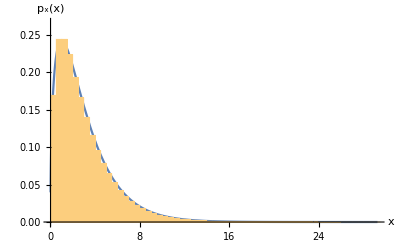

```mathematica
Off[Maximize::wksol]
spoint =Solve[PDF[𝒟,x]==3 10^-3][[All,1,2]][[2]];
h1= Histogram[vals,75,"PDF",ChartLegends->Placed[SwatchLegend[{"Hist"}],Scaled[{.5,1}]],PerformanceGoal->"Speed",PlotRange->{{Min[vals],Max[vals]},{0,1.1Maximize[PDF[𝒟,x],x][[1]]}},AxesLabel-> {"x","p_x(x)"}];
h3= Histogram[vals,75,"PDF",PlotRange->{{spoint,Max[vals]},{0,5 10^-3}},PlotRangePadding->Automatic,PerformanceGoal->"Speed",AxesOrigin->{Max[vals]*.85+spoint*.1,0},Ticks->{Automatic,Table[{i,ScientificForm[N@i,3]},{i,0,5 10^-3,5 10^-3/2}]}];
h2=Plot[PDF[𝒟,x],{x,Min[vals],Max[vals]},PlotLegends->Placed[LineLegend[{"PDF"}],Scaled[{.5,1}]],PlotRange->{{Min[vals],Max[vals]},{0,1.1Maximize[PDF[𝒟,x],x][[1]]}}];
h4=Plot[PDF[𝒟,x],{x,spoint,Max[vals]}];
pdfPlot=Show[h2,h1,LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],AxesLabel-> {"x","p_x(x)"},TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],
Epilog-> Inset[Show[h3,h4],Scaled[{.8,.65}],Automatic,Automatic]]
```

## Statistical Validation

Since the statistical tests results for correlated sequences (processes) is nontrivial, the processes is down-sampled to uncorrelated (white) process. All the possible tests are applied.

200

{AndersonDarling,CramerVonMises,KolmogorovSmirnov,Kuiper,PearsonChiSquare,WatsonUSquare}

{The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is rejected at the 0.1 percent level based on the Anderson-Darling test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is rejected at the 0.1 percent level based on the Cramér-von Mises test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is rejected at the 0.1 percent level based on the Kolmogorov-Smirnov test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is rejected at the 0.1 percent level based on the Kuiper test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Pearson χ^2 test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is rejected at the 0.1 percent level based on the Watson U^2 test.}

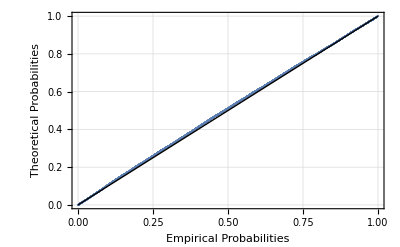

-Graphics-

```mathematica
step = Round[1/(λ Δt)]
tests = DistributionFitTest[vals[[1;;;;step]],𝒟,"AllTests"]
Table[ToExpression[x<> "Test"] [vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001],{x,tests}]
(*AndersonDarlingTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
CramerVonMisesTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
KolmogorovSmirnovTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
KuiperTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
PearsonChiSquareTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
WatsonUSquareTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]*)
probabilityPlot= ProbabilityPlot[vals[[1;;;;step]],𝒟,FrameLabel->{"Empirical Probabilities", "Theoretical Probabilities"},TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],PlotTheme->"Detailed"]
probabilityPlotQ = QuantilePlot[vals[[1;;;;step/10]],𝒟,FrameLabel->{"Empirical Probabilities", "Theoretical Probabilities"},TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],PlotTheme->"Detailed"]
```

### Optional: Save all the plots

```mathematica
SetDirectory[NotebookDirectory[]];
Export["autocorrelationPlot.png",autocorrelationPlot]; Export["timePlot.png",timePlot];Export["pdfPlot.png",pdfPlot];Export["probabilityPlot.png",probabilityPlot];
Export["QQPlot.png",probabilityPlotQ];
```